```mathematica
(*Changing to your local path*)
dataKappa=Import["C:\Users\qiuli\Documents\我的坚果云\codes\others\IAMfit\data\data_kappa.csv"];
```

```mathematica
Transpose[dataKappa][[1]][[2;;]]
```

{634.684,635.684,636.684,637.684,638.684,639.684,640.684,641.684,642.684,643.684,644.684,645.684,646.684,647.684,648.684,649.684,650.684,651.684,652.684,653.684,654.684,655.684,656.684,657.684,658.684,659.684,660.684,661.684,662.684,663.684,664.684,665.684,666.684,667.684,668.684,669.684,670.684,671.684,672.684,673.684,674.684,675.684,676.684,677.684,678.684,679.684,680.684,681.684,682.684,683.684,684.684,685.684,686.684,687.684,688.684,689.684,690.684,691.684,692.684,693.684,694.684,695.684,696.684,697.684,698.684,699.684,700.684,701.684,702.684,703.684,704.684,705.684,706.684,707.684,708.684,709.684,710.684,711.684,712.684,713.684,714.684,715.684,716.684,717.684,718.684,719.684,720.684,721.684,722.684,723.684,724.684,725.684,726.684,727.684,728.684,729.684,730.684,731.684,732.684,733.684,734.684,735.684,736.684,737.684,738.684,739.684,740.684,741.684,742.684,743.684,744.684,745.684,746.684,747.684,748.684,749.684,750.684,751.684,752.684,753.684,754.684,755.684,756.684,757.684,758.684,759.684,760.684,761.684,762.684,763.684,764.684,765.684,766.684,767.684,768.684,769.684,770.684,771.684,772.684,773.684,774.684,775.684,776.684,777.684,778.684,779.684,780.684,781.684,782.684,783.684,784.684,785.684,786.684,787.684,788.684,789.684,790.684,791.684,792.684,793.684,794.684,795.684,796.684,797.684,798.684,799.684,800.684,801.684,802.684,803.684,804.684,805.684,806.684,807.684,808.684,809.684,810.684,811.684,812.684,813.684,814.684,815.684,816.684,817.684,818.684,819.684,820.684,821.684,822.684,823.684,824.684,825.684,826.684,827.684,828.684,829.684,830.684,831.684,832.684,833.684,834.684,835.684,836.684,837.684,838.684,839.684,840.684,841.684,842.684,843.684,844.684,845.684,846.684,847.684,848.684,849.684,850.684,851.684,852.684,853.684,854.684,855.684,856.684,857.684,858.684,859.684,860.684,861.684,862.684,863.684,864.684,865.684,866.684,867.684,868.684,869.684,870.684,871.684,872.684,873.684,874.684,875.684,876.684,877.684,878.684,879.684,880.684,881.684,882.684,883.684,884.684,885.684,886.684,887.684,888.684,889.684,890.684,891.684,892.684,893.684,894.684,895.684,896.684,897.684,898.684,899.684,900.684,901.684,902.684,903.684,904.684,905.684,906.684,907.684,908.684,909.684,910.684,911.684,912.684,913.684,914.684,915.684,916.684,917.684,918.684,919.684,920.684,921.684,922.684,923.684,924.684,925.684,926.684,927.684,928.684,929.684,930.684,931.684,932.684,933.684,934.684,935.684,936.684,937.684,938.684,939.684,940.684,941.684,942.684,943.684,944.684,945.684,946.684,947.684,948.684,949.684,950.684,951.684,952.684,953.684,954.684,955.684,956.684,957.684,958.684,959.684,960.684,961.684,962.684,963.684,964.684,965.684,966.684,967.684,968.684,969.684,970.684,971.684,972.684,973.684,974.684,975.684,976.684,977.684,978.684,979.684,980.684,981.684,982.684,983.684,984.684,985.684,986.684,987.684,988.684,989.684,990.684,991.684,992.684,993.684,994.684,995.684,996.684,997.684,998.684,999.684,1000.68,1001.68,1002.68,1003.68,1004.68,1005.68,1006.68,1007.68,1008.68,1009.68,1010.68,1011.68,1012.68,1013.68,1014.68,1015.68,1016.68,1017.68,1018.68,1019.68,1020.68,1021.68,1022.68,1023.68,1024.68,1025.68,1026.68,1027.68,1028.68,1029.68,1030.68,1031.68,1032.68,1033.68,1034.68,1035.68,1036.68,1037.68,1038.68,1039.68,1040.68,1041.68,1042.68,1043.68,1044.68,1045.68,1046.68,1047.68,1048.68,1049.68,1050.68,1051.68,1052.68,1053.68,1054.68,1055.68,1056.68,1057.68,1058.68,1059.68,1060.68,1061.68,1062.68,1063.68,1064.68,1065.68,1066.68,1067.68,1068.68,1069.68,1070.68,1071.68,1072.68,1073.68,1074.68,1075.68,1076.68,1077.68,1078.68,1079.68,1080.68,1081.68,1082.68,1083.68,1084.68,1085.68,1086.68,1087.68,1088.68,1089.68,1090.68,1091.68,1092.68,1093.68,1094.68,1095.68,1096.68,1097.68,1098.68,1099.68,1100.68,1101.68,1102.68,1103.68,1104.68,1105.68,1106.68,1107.68,1108.68,1109.68,1110.68,1111.68,1112.68,1113.68,1114.68,1115.68,1116.68,1117.68,1118.68,1119.68,1120.68,1121.68,1122.68,1123.68,1124.68,1125.68,1126.68,1127.68,1128.68,1129.68,1130.68,1131.68,1132.68,1133.68,1134.68,1135.68,1136.68,1137.68,1138.68,1139.68,1140.68,1141.68,1142.68,1143.68,1144.68,1145.68,1146.68,1147.68,1148.68,1149.68,1150.68,1151.68,1152.68,1153.68,1154.68,1155.68,1156.68,1157.68,1158.68,1159.68,1160.68,1161.68,1162.68,1163.68,1164.68,1165.68,1166.68,1167.68,1168.68,1169.68,1170.68,1171.68,1172.68,1173.68,1174.68,1175.68,1176.68,1177.68,1178.68,1179.68,1180.68,1181.68,1182.68,1183.68,1184.68,1185.68,1186.68,1187.68,1188.68,1189.68,1190.68,1191.68,1192.68,1193.68,1194.68,1195.68,1196.68,1197.68,1198.68,1199.68,1200.68,1201.68,1202.68,1203.68,1204.68,1205.68,1206.68,1207.68,1208.68,1209.68,1210.68,1211.68,1212.68,1213.68,1214.68,1215.68,1216.68,1217.68,1218.68,1219.68,1220.68,1221.68,1222.68,1223.68,1224.68,1225.68,1226.68,1227.68,1228.68,1229.68,1230.68,1231.68,1232.68,1233.68,1234.68,1235.68,1236.68,1237.68,1238.68,1239.68,1240.68,1241.68,1242.68,1243.68,1244.68,1245.68,1246.68,1247.68,1248.68,1249.68,1250.68,1251.68,1252.68,1253.68,1254.68,1255.68,1256.68,1257.68,1258.68,1259.68,1260.68,1261.68,1262.68,1263.68,1264.68,1265.68,1266.68,1267.68,1268.68,1269.68,1270.68,1271.68,1272.68,1273.68,1274.68,1275.68,1276.68,1277.68,1278.68,1279.68,1280.68,1281.68,1282.68,1283.68,1284.68,1285.68,1286.68,1287.68,1288.68,1289.68,1290.68,1291.68,1292.68,1293.68,1294.68,1295.68,1296.68,1297.68,1298.68,1299.68,1300.68,1301.68,1302.68,1303.68,1304.68,1305.68,1306.68,1307.68,1308.68,1309.68,1310.68,1311.68,1312.68,1313.68,1314.68,1315.68,1316.68,1317.68,1318.68,1319.68,1320.68,1321.68,1322.68,1323.68,1324.68,1325.68,1326.68,1327.68,1328.68,1329.68,1330.68,1331.68,1332.68,1333.68,1334.68,1335.68,1336.68,1337.68,1338.68,1339.68,1340.68,1341.68,1342.68,1343.68,1344.68,1345.68,1346.68,1347.68,1348.68,1349.68,1350.68,1351.68,1352.68,1353.68,1354.68,1355.68,1356.68,1357.68,1358.68,1359.68,1360.68,1361.68,1362.68,1363.68,1364.68,1365.68,1366.68,1367.68,1368.68,1369.68,1370.68,1371.68,1372.68,1373.68,1374.68,1375.68,1376.68,1377.68,1378.68,1379.68,1380.68,1381.68,1382.68,1383.68,1384.68,1385.68,1386.68,1387.68,1388.68,1389.68,1390.68,1391.68,1392.68,1393.68,1394.68,1395.68,1396.68,1397.68,1398.68,1399.68}

```mathematica
Module[{wv,rev,imv},
wv=Transpose[dataKappa][[1]][[2;;]];
rev=Transpose[dataKappa][[2]][[2;;]];
imv=Transpose[dataKappa][[3]][[2;;]];
propKappaRe=Interpolation[Transpose[{wv,rev}]];
propKappaIm=Interpolation[Transpose[{wv,imv}]];
]
```

```mathematica
propKappa[w_]:=propKappaRe[w]+I*propKappaIm[w]
```

InterpolatingFunction::dmval: Input value {633.016} lies outside the range of data in the interpolating function. Extrapolation will be used.

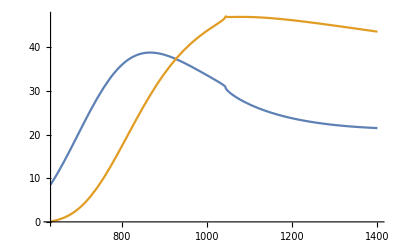

```mathematica
Plot[{propKappaRe[w],propKappaIm[w]},{w,633,1400}]
```